```mathematica
Light Scattering by a Spherical Particle for Mathematica 8
```

8 a by for Light Mathematica Particle Scattering Spherical

## Usage Notes

Date: 		Last Modification: 05/17/12
		Mathematica Version 8.0.10
		
Author:	Guy Mongelli
	  
	  	University of Rochester
	  	Dept. of Chemical Engineering
	  	Rochester, NY 14627
	  	mongelli@che.rochester.edu

Application:
	This notebook calculates and plots the scattering, absorption, and extinction properties of a spherical particle of known refractive index in a suspending medium, also of known index.  The particle is illuminated by an unpolarized or linearly polarized  plane wave of unit amplitude.  The code derives from expositions of the problem in Principles of Optics by Born and Wolf, Absorption and Scattering of Light by Small Particles by Bohren and Huffman, and Light Scattering by Small Particles  by H.C. van de Hulst.  It is capable of calculating the spectral properties of such a particle if the dispersion of both the particle and suspending medium are known.  Similarly, absorptive suspending media are allowable when the complex refractive index is provided.

Layout:
	Parameters such as cross sections, phase functions, efficiency factors, etc. may be calculated and displayed.

## Model Parameters

This section is devoted to entering the known parameters for the problem (i.e., complex indices of refraction, wavelength of the illuminating radiation, sphere radius, etc.).  Subscripts of 1 correspond to the embedding medium and subscripts of 2 represent the sphere.  It is assumed by H.C. van de Hulst that neither the medium nor the particle is magnetic (or at very least they have the same permeability).  Notice that the imaginary part of the refractive index is represented by a lower case k, and that capital K represents the wave number.  Finally, it would be more efficient to assign the parameter values (lambda of excitation, radius, real and imaginary index) using rewrite rules in the actual function calls but I've presented them as constants because this format is more readable.

```mathematica
Subscript[n, 1] = 1.3;                             (* Real part of refractive index of medium *)
Subscript[n, 2] =.2;            (* Real part of refractive index of scatterer *)
Subscript[k, 1] = 0*10^-2 ;                (* Imag"inary part of refractive index of medium **)
Subscript[k, 2] = 3.6;                 (* Imaginary part of refractive index of scatterer *)
Subscript[λ, 0] = 544543 * 10^-6;   (* Vacuum wavelength in μm *)
r =.1              (*Sphere radius in μm *);
```

Required derived quantities for given parameter set.

```mathematica
Subscript[m, 1] = Subscript[n, 1] + I Subscript[k, 1]  ;               (* Complex refractive index of medium *)
Subscript[m, 2] = Subscript[n, 2] + I Subscript[k, 2]  ;             (* Complex refractive index of scatterer *)
Subscript[m, Rel] = (Subscript[n, 2] + I Subscript[k, 2])/(Subscript[n, 1] + I Subscript[k, 1]) ;          (* Relative refractive index between scatterer and medium *)
Subscript[λ, 1] =Subscript[λ, 0]/(Subscript[n, 1] + I Subscript[k, 1]);               (* Wavelength in external medium in μm *)
Subscript[λ, 2] =Subscript[λ, 0]/(Subscript[n, 2] + I Subscript[k, 2]) ;              (* Wavelength inside sphere in μm *)
Subscript[K, 0] =  (2 π)/Subscript[λ, 0];                         (* Wave number in vacuum in μm^-1 *)
Subscript[K, 1] =  (2 π)/Subscript[λ, 1];                         (* Wave number in external medium in μm^-1 *)
Subscript[K, 2] =  (2 π)/Subscript[λ, 2]                          (* Wave number inside the sphere in μm^-1*) ;
```

```mathematica
Subscript[m, 1]            (* Complex refractive index of medium *)
Subscript[m, 2]            (* Complex refractive index of scatterer *)
Subscript[m, Rel]           (* Relative refractive index between scatterer and medium *)
Subscript[λ, 1]               (* Wavelength in external medium in μm *)
Subscript[λ, 2]               (* Wavelength inside sphere in μm *)
Subscript[K, 0]                (* Wave number in vacuum in μm^-1 *)
Subscript[K, 1]                  (* Wave number in external medium in μm^-1 *)
Subscript[K, 2]              (* Wave number inside the sphere in μm^-1*)
```

1.3

0.2+3.6 ⅈ

0.153846+2.76923 ⅈ

0.418879

0.00837758-0.150797 ⅈ

(2000000 π)/544543

15.

2.30769+41.5384 ⅈ

Now create the size parameter.  Note there are actually three size parameters defined (as opposed to Bohren and Huffman's single size parameter), two of which are now complex and due to the fact that the external medium may be absorptive.  They come from the paper by Fu and Sun (Applied Optics, Vol. 40, No. 9, 2001,pp. 1354-1361) which explains how to treat a particle in an absorbing medium.  They are used subsequently to determine how many terms are maintained in the series defining the scattered intensity, cross sections, efficiencies, asymmetry factor, etc., and also serve as arguments to the scattering coefficient equations.  They are set up as functions of particle radius so that this may be varied and plots vs. radius (or q parameter) can be examined.

```mathematica
q[a_] := Subscript[K, 0] a
Subscript[q, 1][a_] :=Subscript[K, 1] a 
Subscript[q, 2][a_] :=Subscript[K, 2] a 

Print["The size parameter is ",q[r]//N]
Print["The external size parameter is ",Subscript[q, 1][r]//N]
Print["The internal size parameter is ",Subscript[q, 2][r]//N]
```

The size parameter is 1.15385

The external size parameter is 1.5

The internal size parameter is 0.230769+4.15384 ⅈ

I use the equation suggested by Wiscombe [Applied Optics, Vol. 19, (1980) page 1505] for obtaining the series solution termination point for a given size parameter.  Since there are now three (two possibly complex) size parameters, I choose the largest of the absolute values of the three as the argument to the equation.  The equation was found to be valid for the range 8 < q < 4200.  For smaller q values, the suggestion is LastTerm = q + 4 q^(1/3) +1.  I don't suggest trying to run the program for very large size parameters due to the resulting long computation times (in fact, anything over q=100 becomes tediously long).

```mathematica
Largest[a_] :=Max[q[a],Abs[Subscript[q, 1][a]],Abs[Subscript[q, 2][a]]]
LastTerm[a_]:= Ceiling[Abs[Largest[a] + 4.05 (Largest[a])^(1/3) +2]] ;
Print["The series termination value is ",LastTerm[r], "."]
```

The series termination value is 13.

## Required function definitions

The following defines a "complex conjugate" function.  This allows the familiar  *  notation to be used later when the complex conjugates of certain functions are required.

```mathematica
SuperStar[ϕ_] := ϕ/.Complex[u_, v_] -> Complex[u, -v]
```

The spherical Bessel, Neumann and Hankel functions are used to represent the radial field dependence.   Boundary conditions at r = 0 and r = ∞  require finite fields and hence the need for all three types of Bessel functions.  We go straight to the Ricatti-Bessel functions here by simply multiplying through by ρ.

```mathematica
ψ[l_,ρ_]:= ρ √(π/(2 ρ))  BesselJ[(l + 1/2),ρ ]                                  (* Ricatti-Bessel function of 1st kind. *)  
ψPrime[l_,ρ_]:=Evaluate[D[ ψ[l,ρ],ρ]] ;                                (* Partial derivative of Ricatti-Bessel function w/r/t ρ. *)
ζ[l_,ρ_]:=ψ[l, ρ] + I ρ √(π/(2 ρ)) BesselY[(l + 1/2),ρ ] ;      (* Ricatti-Hankel function *)
ζPrime[l_,ρ_]:=Evaluate[D[ ζ[l,ρ],ρ]];(* Partial derivative of Ricatti-Hankel function  w/r/t/ ρ *)
```

The associated Legendre functions are used for the azimuthal components of the field.  These are built into Mathematica.  Note that the Mathematica version has a (-1)^min front of the function definition, which Born and Wolf do not have (but make mention of).  Here, m is the separation constant that arises from the separation of variables technique used to solve the wave equation and must equal one for this problem.  Since m = 1, we get a negative sign out front so another one is multiplied out to conform to the actual field.  Then, these are used to construct the "angle function" coefficients π_n and τ_n. They are derived from the Legendre functions as shown below.  Note the final argument to the Legendre polynomial is actually cos(θ).

```mathematica
pi[i_, θ_] :=  LegendreP[i,1,Cos[θ]]/Sin[θ]; 
τ[i_, θ_]:= D[ LegendreP[i,1,Cos[θ]],θ];
```

```mathematica
These are complex functions so they are not represented well in the real plane here.  I will need to plot them in the complex plane.
```

```mathematica
TableForm[N[Table[{ψ[l, Subscript[q, 1][r]],ψPrime[l, Subscript[q, 1][r]] , ζ[l,Subscript[q, 1][r]],ζPrime[l, Subscript[q, 1][r]]},{l,1,5}],6], TableHeadings-> {Automatic,{"ψ[l, q_1]","ψ'[l, q_1]","ζ[l, q_1]","ζ'[l, q_1]"} }]
```

| ψ[l, q_1] | ψ'[l, q_1] | ζ[l, q_1] | ζ'[l, q_1]
1 | 0.594259 | 0.601322 | 0.594259-1.04465 ⅈ | 0.601322+0.625698 ⅈ
2 | 0.191024 | 0.339561 | 0.191024-2.01857 ⅈ | 0.339561+1.64677 ⅈ
3 | 0.0424869 | 0.10605 | 0.0424869-5.68392 ⅈ | 0.10605+9.34927 ⅈ
4 | 0.00724855 | 0.0231574 | 0.00724855-24.5064 ⅈ | 0.0231574+59.6665 ⅈ
5 | 0.00100443 | 0.00390045 | 0.00100443-141.355 ⅈ | 0.00390045+446.676 ⅈ

```mathematica
TableForm[N[Table[{ψ[l, Subscript[q, 2][r]],ψPrime[l, Subscript[q, 2][r]] , ζ[l, Subscript[q, 2][r]],ζPrime[l, Subscript[q, 2][r]]},{l,1,5}],6], TableHeadings-> {Automatic,{"ψ[l, q_2]","ψ'[l, q_2]","ζ[l, q_2]","ζ'[l, q_2]"} }]
```

| ψ[l, q_2] | ψ'[l, q_2] | ζ[l, q_2] | ζ'[l, q_2]
1 | -23.4686+5.9456 ⅈ | 6.17022+25.2757 ⅈ | -0.0189088-0.0046578 ⅈ | 0.00496189-0.0197636 ⅈ
2 | -3.94216-13.8522 ⅈ | -16.7145+4.42276 ⅈ | -0.00770187+0.0287156 ⅈ | -0.0324869-0.00912044 ⅈ
3 | 6.58316-2.13849 ⅈ | -2.66577-9.02681 ⅈ | 0.0528541+0.0158144 ⅈ | -0.0212024+0.0661381 ⅈ
4 | 0.963919+2.59292 ⅈ | 4.04255-1.35142 ⅈ | 0.0392032-0.116035 ⅈ | 0.162157+0.059638 ⅈ
5 | -0.866785+0.367576 ⅈ | 0.580614+1.52827 ⅈ | -0.298785-0.114417 ⅈ | 0.196423-0.466948 ⅈ

#### We now have enough information to construct the Mie coefficients.

```mathematica
an[l_, a_]:=Evaluate[(Subscript[m, 2] ψPrime [ l,Subscript[q, 1][a]]  ψ[l,Subscript[q, 2][a]] - Subscript[m, 1] ψ[l,Subscript[q, 1][a]]  ψPrime [ l,Subscript[q, 2][a]])/(Subscript[m, 2] ζPrime[l, Subscript[q, 1][a]]  ψ[l, Subscript[q, 2][a]] - Subscript[m, 1] ζ[l,Subscript[q, 1][a]]  ψPrime[l, Subscript[q, 2][a]] )]

bn[l_, a_]:=Evaluate[(Subscript[m, 2] ψ[l,Subscript[q, 1][a]] ψPrime [ l,Subscript[q, 2][a]] - Subscript[m, 1] ψPrime [ l,Subscript[q, 1][a]] ψ[l, Subscript[q, 2][a]] )/(Subscript[m, 2] ζ[l, Subscript[q, 1][a]] ψPrime[l, Subscript[q, 2][a]] - Subscript[m, 1]  ζPrime[l,Subscript[q, 1][a]] ψ[l, Subscript[q, 2][a]])]

cn[l_, a_]:=Evaluate[ (Subscript[m, 2]  ζ[l,Subscript[q, 1][a]]ψPrime [ l,Subscript[q, 1][a]]  - Subscript[m, 2]  ζPrime[l,Subscript[q, 1][a]]ψ[l,Subscript[q, 1][a]])/(Subscript[m, 2] ζ[l, Subscript[q, 1][a]] ψPrime[l, Subscript[q, 2][a]] - Subscript[m, 1]  ζPrime[l,Subscript[q, 1][a]] ψ[l, Subscript[q, 2][a]])]

dn[l_, a_]:=Evaluate[(Subscript[m, 2] ζPrime[l,Subscript[q, 1][a]] ψ[l,Subscript[q, 1][a]] - Subscript[m, 2] ζ [ l,Subscript[q, 1][a]] ψPrime[l, Subscript[q, 1][a]] )/(Subscript[m, 2] ζPrime[l, Subscript[q, 1][a]] ψ[l, Subscript[q, 2][a]] - Subscript[m, 1] ζ[l,Subscript[q, 1][a]] ψPrime[l, Subscript[q, 2][a]]  )]
```

Again, display the first few coefficients.

```mathematica
TableForm[N[Table[{an[l,r],bn[l,r],cn[l,r],dn[l,r]},{l,1,5}]], TableHeadings-> {Automatic,{"a_n[l]","b_n[l]","c_n[l]","d_n[l]" }}]
```

| a_n[l] | b_n[l] | c_n[l] | d_n[l]
1 | 0.905504-0.232651 ⅈ | 0.096651+0.279974 ⅈ | -0.00199612-0.0289091 ⅈ | -0.000981915-0.0464463 ⅈ
2 | 0.247927-0.385578 ⅈ | 0.00300101+0.0352807 ⅈ | -0.022428-0.00492218 ⅈ | -0.0558628+0.0506604 ⅈ
3 | 0.00130254-0.0192198 ⅈ | 0.000116755+0.0017603 ⅈ | -0.00355578+0.0125201 ⅈ | 0.0204738+0.00789942 ⅈ
4 | 0.0000235076-0.000588639 ⅈ | 3.51255×10^-6+0.0000475768 ⅈ | 0.00579987+0.00188677 ⅈ | 0.00292676-0.00727082 ⅈ
5 | 4.54593×10^-7-0.0000126136 ⅈ | 6.62715×10^-8+8.31066×10^-7 ⅈ | 0.000911036-0.00244899 ⅈ | -0.002699-0.00121871 ⅈ

Now we create a pair of intermediate functions to simplify the cross section and phase function equations below.  They also prove helpful when calculating the scattering matrix elements.

```mathematica
A[l_, a_] :=1/Subscript[K, 2]((Abs[cn[l,a]])^2  ψ[l, Subscript[q, 2][a]] SuperStar[ψPrime[l,  Subscript[q, 2][a]]] -  (Abs[dn[l,a]])^2 ψPrime[l,  Subscript[q, 2][a]] SuperStar[ψ[l,  Subscript[q, 2][a]]])

B[l_, a_]:=1/Subscript[K, 1]((Abs[an[l,a]])^2  ζPrime[l, Subscript[q, 1][a]] SuperStar[ζ[l, Subscript[q, 1][a]]] -  (Abs[bn[l,a]])^2 ζ[l, Subscript[q, 1][a]] SuperStar[ζPrime[l, Subscript[q, 1][a]]])
```

Tabulate some of these coefficients.

```mathematica
TableForm[N[Table[{A[l,r] ,B[l,r]},{l,1,5}]], TableHeadings-> {Automatic,{"A[l]","B[l]"} }]
```

| A[l] | B[l]
1 | 0.0453101+0.00269094 ⅈ | -0.0155326+0.0641194 ⅈ
2 | 0.0371004+0.00263577 ⅈ | -0.0453873+0.0140928 ⅈ
3 | 0.00101675+0.0000696725 ⅈ | -0.00130354+0.0000249472 ⅈ
4 | 0.0000278828+1.77806×10^-6 ⅈ | -0.0000336086+2.32883×10^-8 ⅈ
5 | 5.75617×10^-7+3.47136×10^-8 ⅈ | -6.67663×10^-7+1.06671×10^-11 ⅈ

Finally, create an equation to determine the average intensity incident on the sphere. The function for the average intensity comes from the Fu and Sun paper and is set up as a conditional since the general form will crash when k_1= 0 (nonabsorbing external medium).  In that case, the limit of the function as k_1→ 0 is used.

```mathematica
ILimit[a_] := Limit[(Subscript[λ, 0])^2/(8 π (k)^2) Subscript[n, 1]/(2 (3*10^8))(1 + ((4 π a k)/Subscript[λ, 0] - 1)Exp[(4 π a k)/Subscript[λ, 0]]), k -> 0]
```

```mathematica
f[a_] := If[Subscript[k, 1] ≠ 0, N[((Subscript[λ, 0])^2/(8 π (Subscript[k, 1])^2)Subscript[n, 1]/(2 (3*10^8))(1 + ((4 π a Subscript[k, 1])/Subscript[λ, 0] - 1)Exp[(4 π a Subscript[k, 1])/Subscript[λ, 0]]))], ILimit[a]]
```

## Calculate and plot the cross sections

Here are the actual cross section equations.  Note that the Fu and Sun technique allows direct analytical determination of the absorption cross section.

```mathematica
CScat[a_]:=  (π a^2)/f[a] * (π Subscript[λ, 0])/(2π (3* 10^8))  ∑_(l=1)^(LastTerm[a]*2) (2 l+1)  Im[B[l,a]]
CAbs[a_]:=(π a^2)/f[a] * (π Subscript[λ, 0])/(2π (3* 10^8)) ∑_(l=1)^(LastTerm[a]*2) (2 l+1) Im[A[l,a]]
CExt[a_]:=(π a^2)/f[a] * (π Subscript[λ, 0])/(2π (3* 10^8)) ∑_(l=1)^(LastTerm[a]*2) (2 l+1) Im[A[l,a] + B[l,a]]
```

Print out cross sections for the default parameters.

```mathematica
Print["C_Scat = ", CScat[r]//N, " μm^2",  
	  "\nC_Abs = ", CAbs[r]//N," μm^2",
           "\nC_Ext = ", CExt[r]//N," μm^2" ]
```

C_Scat = 0.110164 μm^2
C_Abs = 0.00911305 μm^2
C_Ext = 0.119277 μm^2

#### Linear plots of size parameter vs. cross section.

These plots take longer to generate as the size parameter increases.  Also, the multiplicative factor in the argument converts the range variable to q values rather than radius values.  This first cell sets up some default plotting parameters.

```mathematica
SetOptions[Plot, Frame-> True, PlotRange-> All, ImageSize-> 700, GridLines-> Automatic,PlotPoints-> 40];
```

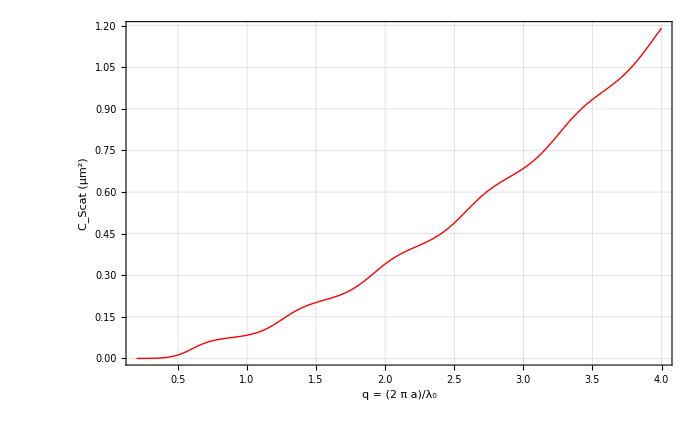

```mathematica
CScatPlot = Plot[CScat[i Subscript[λ, 0]/(2π)], {i,.2,4},  PlotStyle-> RGBColor[1,0,0],FrameLabel-> {"q = (2  π a)/λ_0", "C_Scat  (μm^2)"} ]
```

```mathematica
So by decreasing the wavelegnth (bluer)for a given particle size, we increase the size paramater and therefore increase the scattering crossection.
```

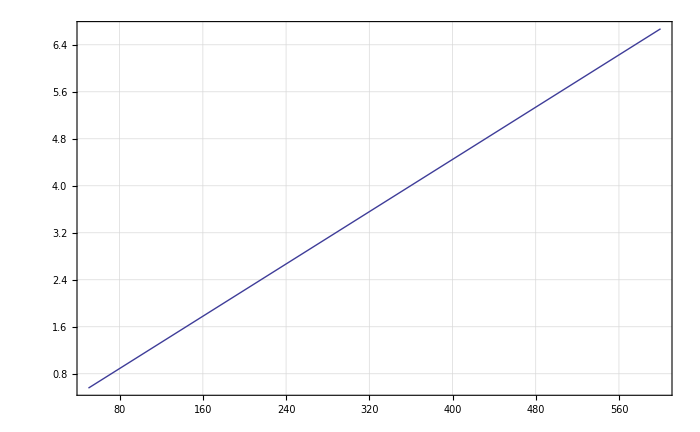

```mathematica
Plot[2*Pi*size/565,{size,50,600}]
```

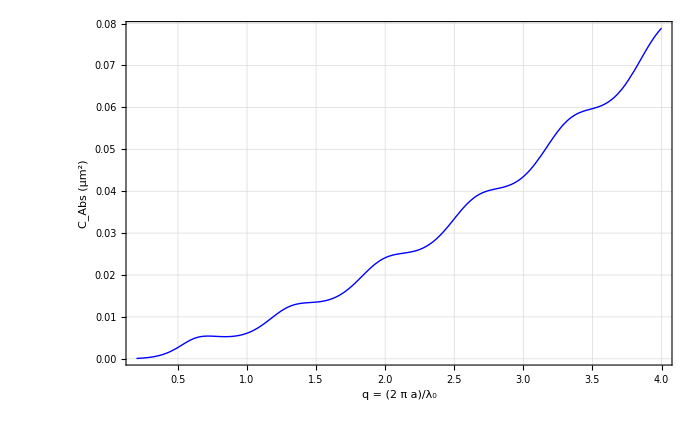

```mathematica
CAbsPlot = Plot[CAbs[i Subscript[λ, 0]/(2π)], {i, .2, 4}, PlotStyle-> RGBColor[0,0,1],FrameLabel-> {"q = (2  π a)/λ_0", "C_Abs  (μm^2)"}]
```

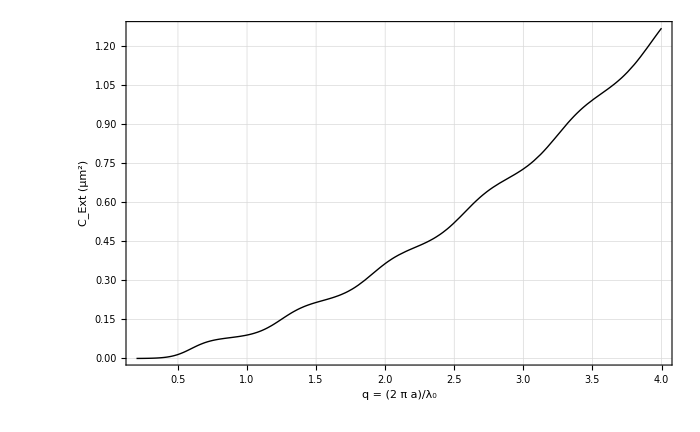

```mathematica
CExtPlot = Plot[CExt[i Subscript[λ, 0]/(2π)], {i,.2,4}, PlotStyle-> RGBColor[0,0,0], FrameLabel-> {"q = (2  π a)/λ_0", "C_Ext  (μm^2)"}]
```

All three on the same plot.  The first cell creates a legend for the plot.

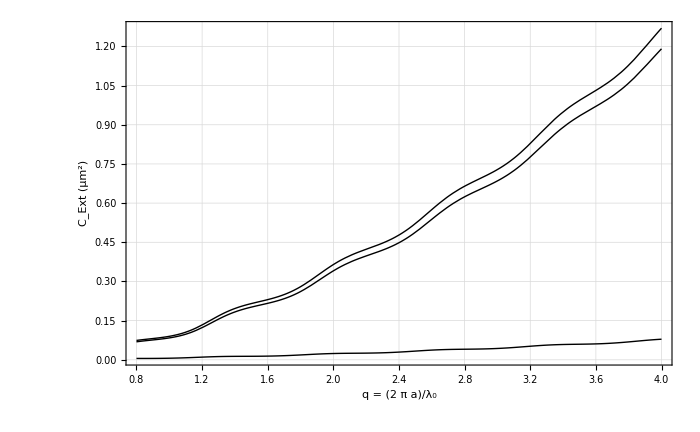

```mathematica
Plot[{CExt[i Subscript[λ, 0]/(2π)],CAbs[i Subscript[λ, 0]/(2π)],CScat[i Subscript[λ, 0]/(2π)]}, {i, .8,4}, PlotStyle-> RGBColor[0,0,0], FrameLabel-> {"q = (2  π a)/λ_0", "C_Ext  (μm^2)"}]
```

```mathematica
(* CLegend = {{{RGBColor[1,0,0],"C_scat"},{RGBColor[0,0,1],"C_abs"},{RGBColor[0,0,0],"C_ext"}}, LegendPosition-> {-.55,0.3}, LegendSize-> {0.25,0.25}, LegendShadow-> {0,0}};
```

```mathematica
(* ShowLegend[Show[CScatPlot,CAbsPlot,CExtPlot, DisplayFunction-> Identity], CLegend,DisplayFunction-> $DisplayFunction ];
```

## Calculate and plot the efficiencies

The efficiencies are defined simply as the ratio of the cross sections to the geometrical cross sectional area of the scatterer.

```mathematica
QScat[a_]:=  CScat[a]/(π a^2)
QAbs[a_]:= CAbs[a]/(π a^2)
QExt[a_]:=CExt[a]/(π a^2)
```

Print out efficiencies for the default parameters.

```mathematica
Print["Q_Scat = ",QScat[r]//N,"\nQ_Abs = ",QAbs[r]//N,"\nQ_Ext = ",QExt[r]//N ]
```

Q_Scat = 3.50663
Q_Abs = 0.290077
Q_Ext = 3.79671

#### Linear plots of size parameter vs. efficiency.

Note that these plots take longer to generate as the size parameter increases.  The multiplicative factor in the argument converts the abscissa variable to q values (rather than radius values).

```mathematica
SetOptions[Plot, Frame-> True, PlotRange-> All, ImageSize-> 700, GridLines-> Automatic,PlotPoints-> 40];
```

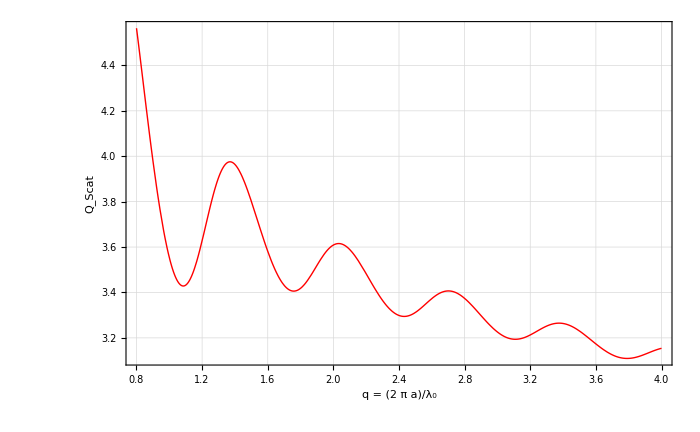

```mathematica
QScatPlot = Plot[QScat[i (Subscript[λ, 0]/(2π) )], {i,.8, 4}, PlotStyle-> RGBColor[1,0,0],  FrameLabel-> {"q = (2  π a)/λ_0", "Q_Scat"}]
```

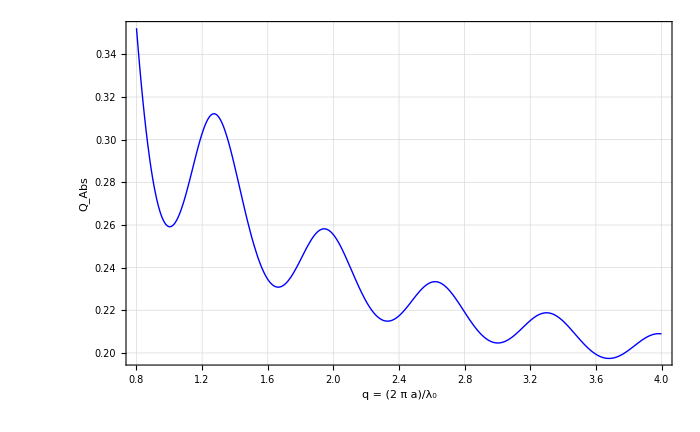

```mathematica
QAbsPlot = Plot[QAbs[i (Subscript[λ, 0]/(2π))], {i, .8, 4}, PlotStyle-> RGBColor[0,0,1], FrameLabel-> {"q = (2  π a)/λ_0", "Q_Abs"}]
```

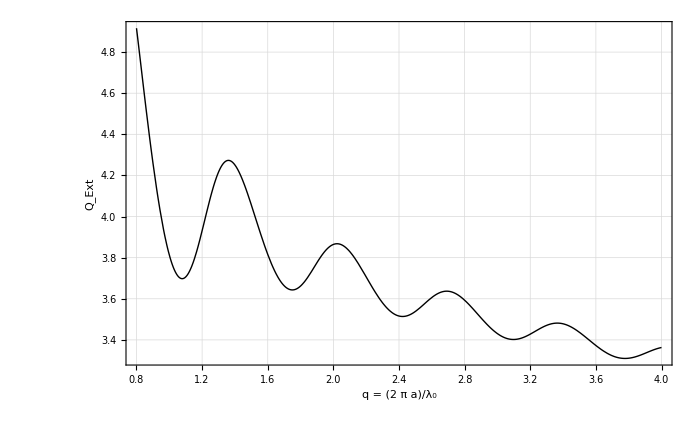

```mathematica
QExtPlot =Plot[QExt[i Subscript[λ, 0]/(2π)], {i, .8, 4}, PlotStyle-> RGBColor[0,0,0], FrameLabel-> {"q = (2  π a)/λ_0", "Q_Ext"}]
```

All three on the same plot.  The first cell creates a legend for the plot.

```mathematica
(* QLegend = {{{RGBColor[1,0,0],"Q_scat"},{RGBColor[0,0,1],"Q_abs"},{RGBColor[0,0,0],"Q_ext"}}, LegendPosition-> {-.55,0.3}, LegendSize-> {0.25,0.25}, LegendShadow-> {0,0}};
```

```mathematica
(* ShowLegend[Show[QScatPlot,QAbsPlot,QExtPlot, PlotRange-> All,DisplayFunction-> Identity], QLegend,DisplayFunction-> $DisplayFunction ];
```

#### Log-linear plots of size parameter vs. efficiency.

These plots are useful when plotting over a large range of q values, but take longer to generate as the size parameter increases.  The multiplicative factor in the argument converts the abscissa variable to q values (rather than radius values).

```mathematica
(* SetOptions[LogLinearPlot, Frame-> True, PlotRange-> All, ImageSize-> 700, GridLines-> Automatic,PlotPoints-> 40];
```

```mathematica
Note from Guy: These scattering efficiencies should be dimensionless but were not coded so by Art Lampado.  I will go through and alter this.
```

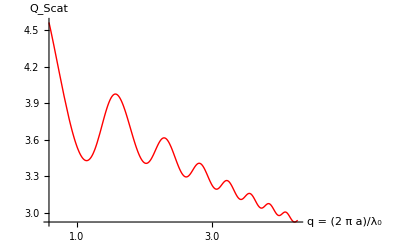

```mathematica
QScatLogPlot = LogLinearPlot[QScat[i (Subscript[λ, 0]/(2π) )], {i,.8, 6}, PlotStyle-> RGBColor[1,0,0],  AxesLabel-> {"q = (2  π a)/λ_0", "Q_Scat"}]
```

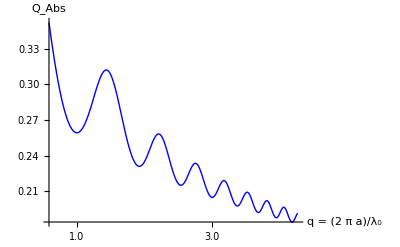

```mathematica
QAbsLogPlot = LogLinearPlot[QAbs[i (Subscript[λ, 0]/(2π))], {i, .8, 6}, PlotStyle-> RGBColor[0,0,1], AxesLabel-> {"q = (2  π a)/λ_0", "Q_Abs"}]
```

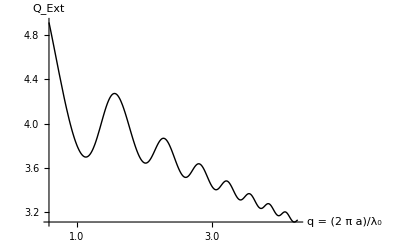

```mathematica
QExtLogPlot = LogLinearPlot[QExt[i Subscript[λ, 0]/(2π)], {i, .8, 6}, PlotStyle-> RGBColor[0,0,0], AxesLabel-> {"q = (2  π a)/λ_0", "Q_Ext"}]
```

All three on the same plot.  The first cell creates a legend for the plot.

```mathematica
QLegend = {{{RGBColor[1,0,0],"Q_scat"},{RGBColor[0,0,1],"Q_abs"},{RGBColor[0,0,0],"Q_ext"}}, LegendPosition-> {-.55,0.3}, LegendSize-> {0.25,0.25}, LegendShadow-> {0,0}};
```

```mathematica
ShowLegend[Show[QScatLogPlot,QAbsLogPlot,QExtLogPlot, PlotRange-> All,DisplayFunction-> Identity], QLegend,DisplayFunction-> $DisplayFunction ];
```

## Calculate and plot the asymmetry factor

The equation for the asymmetry factor comes from Fu and Sun (Applied Optics, Vol. 40, No. 9, 2001, pp. 1354-1361).

```mathematica
g[a_] := (2∑_(l=1)^LastTerm[a] ((l(l+2))/(l + 1) Re[(an[l,a]*  SuperStar[an[l+1,a]]+ bn[l,a]*SuperStar[bn[l+1,a]])] + (2l+1)/(l(l + 1)) Re[(an[l,a] *SuperStar[bn[l,a]])]))/(∑_(l=1)^LastTerm[a] (2l+1)((Abs[an[l,a]])^2 + (Abs[bn[l,a]])^2))
```

```mathematica
StringJoin["The anisotropy value is g = ", ToString[-g[r]//N]]
```

The anisotropy value is g = -0.268813

#### Create plot of size parameter vs. asymmetry factor.

```mathematica
The assummetry factor denotes the symmetry of the phase function and related whether forward scattering or back scattering is dominant (greater than 1 is forward, less than 1 is backscattering).
```

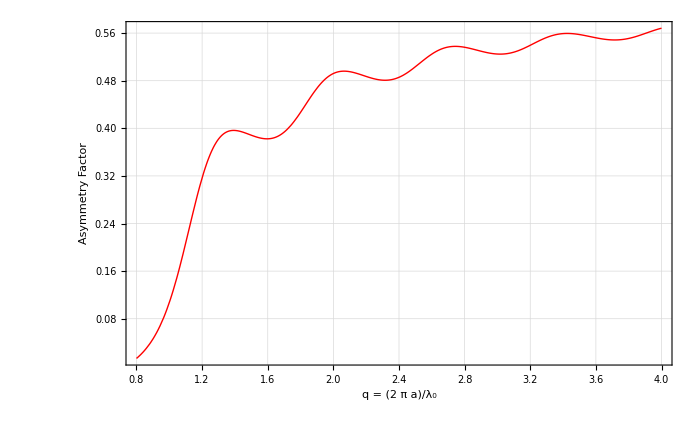

```mathematica
gPlot = Plot[g[i Subscript[λ, 0]/(2π)], {i,.8, 4}, Frame-> True, PlotRange-> All, ImageSize-> 700, PlotStyle-> RGBColor[1,0,0], GridLines-> Automatic, FrameLabel-> {"q = (2  π a)/λ_0", "Asymmetry Factor"}]
```

## Calculate and plot the albedo

The albedo is simply the ratio of the scattering to extinction cross sections.

```mathematica
albedo[a_] := CScat[a]/CExt[a];
StringJoin["The albedo is ", ToString[albedo[r]//N]]
```

The albedo is 0.923598

```mathematica
albedo[r]
```

0.923598

```mathematica
Manipulate[N[albedo[i*Subscript[λ, 0]/(2π)],3],{i,1,6}]
```

#### Create plot of albedo vs. size parameter.

```mathematica
(* SetOptions[LogLinearPlot, Frame-> True, PlotRange-> All, ImageSize-> 700, GridLines-> Automatic,PlotPoints-> 40];
```

```mathematica
(* In the next section of code, i is the size paramater.  *)
```

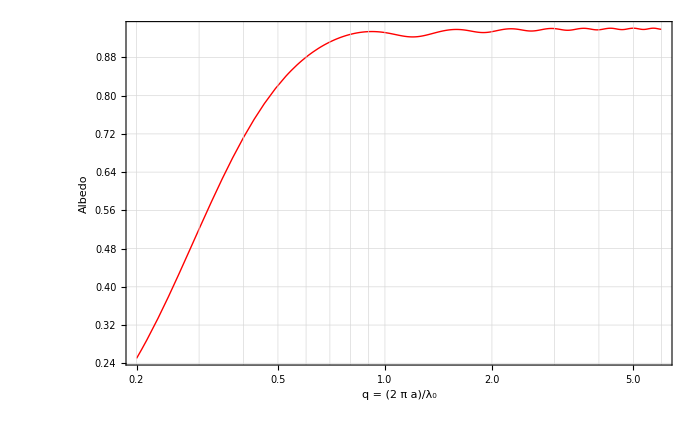

```mathematica
AlbedoPlot = LogLinearPlot[albedo[i Subscript[λ, 0]/(2π)], {i,.2, 6}, Frame-> True, PlotRange-> All, ImageSize-> 700, PlotStyle-> RGBColor[1,0,0], GridLines-> Automatic, FrameLabel-> {"q = (2  π a)/λ_0", "Albedo"}]
```

## Calculate and plot the scattering phase functions

Next, we construct the formulae for intensity as a function of angular position for incident radiation polarized in either of the two linear orthogonal polarization states.  Begin by defining the amplitude matrix elements, S1(r, θ) and S2(r, θ) which simplify the form of the resulting phase function equations a little

```mathematica
S1[a_,θ_]:= ∑_(l=1)^LastTerm[a] ((2 l+1)/(l (l+1)))(an[l,a]pi[l,θ]+bn[l,a]  τ[l,θ]);
S2[a_,θ_]:= ∑_(l=1)^LastTerm[a] ((2 l+1)/(l (l+1)))( an[l,a] τ[l,θ]+bn[l,a]  pi[l,θ] );
```

```mathematica
(* Added by Guy *)
```

```mathematica
(* Look at the phase difference between the scattered beams A and B
```

```mathematica
(* N[(Re[S1[a,θ]]Im[S2[a,θ]]-Re[S2[a,θ]]Im[S1[a, θ]])/(Re[S1[a,θ]]Re[S2[a,θ]]+Im[S1[a,θ]]Im[S2[a, θ]]),3]
```

```mathematica
(*  θ1=ContourPlot[N[(Re[S1[a, θ]]Im[S2[a, θ]]-Re[S2[a, θ]]Im[S1[a, θ]])/(Re[S1[a, θ]]Re[S2[a, θ]]+Im[S1[a, θ]]Im[S2[a, θ]]),3],{a,0,1},{θ,0,.9π}]
```

```mathematica
Look at the scattering amplitude in the forward direction:
```

```mathematica
Cextfor=(Subscript[λ, 0]^2/Pi)*Re[S[1,0]]
```

(296527078849 Re[S[1,0]])/(1000000000000 π)

Here are the phase function equations.  The normalization factor (to insure ∫P(cos(θ))ⅆΩ =  1) is sometime used in the literature (e.g., Fu and Sun) and sometimes neglected (e.g Bohren and Huffman).  Therefore, two separate functions for the unpolarized scattering phase function are created and either one may be used.

```mathematica
Iperp[a_, θ_]:= (Abs[S1[a,θ]])^2;

Ipar[a_, θ_]:= (Abs[S2[a,θ]])^2;

Iunpol[a_, θ_]:= (Iperp[a, θ] + Ipar[a, θ])/2;

Norma[a_]:=∑_(l=1)^LastTerm[a] 2(l + 1)((Abs[an[l,a]])^2 + (Abs[bn[l,a]])^2)

IunpolNorm[a_, θ_]:= (Iperp[a, θ] + Ipar[a, θ])/Norma[a];
```

### Create plots of the phase functions.

#### Log-linear plots of scattered intensity vs. angle.

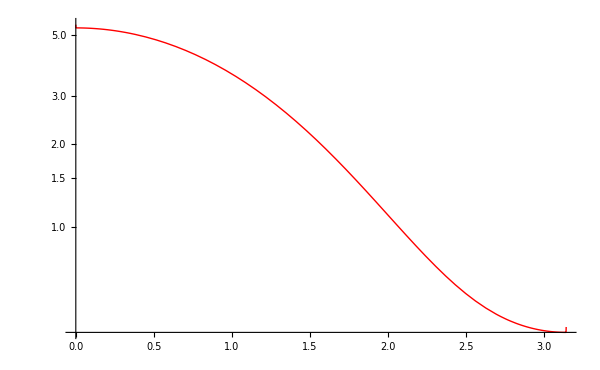

```mathematica
IPerpPlot = LogPlot[Evaluate[Iperp[r, θ]], {θ, 0, π},  PlotStyle-> RGBColor[1,0,0],  FrameLabel-> {"θ (deg)", "I_perp Phase Function"}]
```

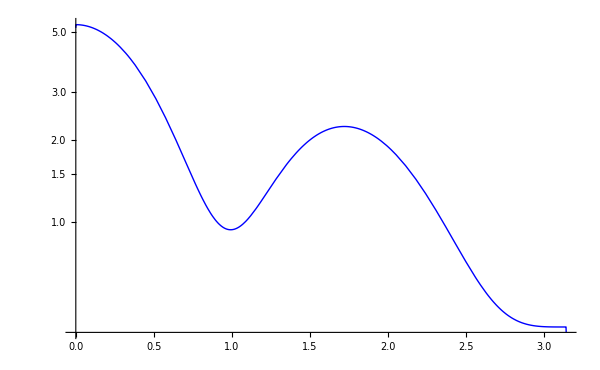

```mathematica
IParPlot = LogPlot[Evaluate[Ipar[r, θ]], {θ, 0, π},  PlotStyle-> RGBColor[0,0,1],  FrameLabel-> {"θ (deg)", "I_par Phase Function"}]
```

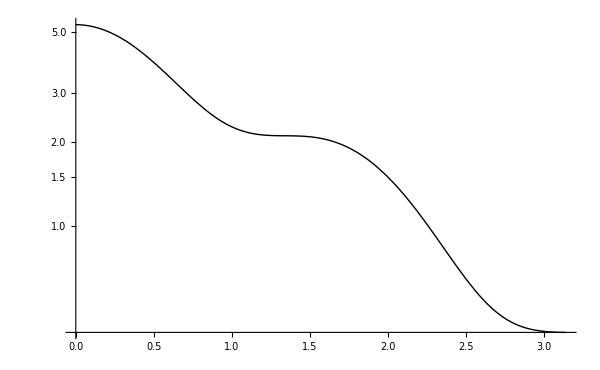

```mathematica
IUnpolPlot = LogPlot[Evaluate[Iunpol[r, θ]], {θ, 0, π},  PlotStyle-> RGBColor[0,0,0],  FrameLabel-> {"θ (deg)", "I_unpol Phase Function"}]
```

All three on the same plot.  The first expression creates a legend for the plot.

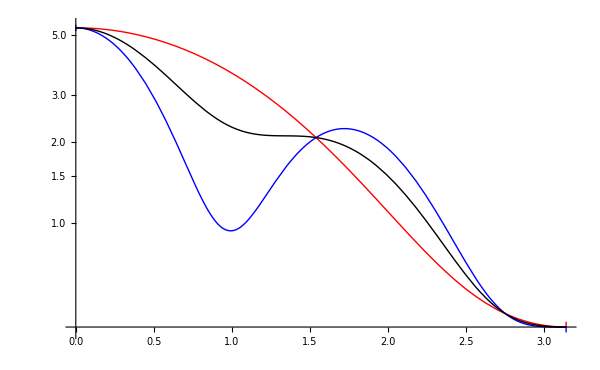

```mathematica
ILegend = {{{RGBColor[1,0,0],"I_perp"},{RGBColor[0,0,1],"I_par"},{RGBColor[0,0,0],"I_unpol"}}, LegendPosition-> {.5,0.3}, LegendSize-> {0.25,0.25}, LegendShadow-> {0,0}};
Show[IPerpPlot,IParPlot,IUnpolPlot, PlotRange-> All,DisplayFunction-> Identity, FrameLabel->{"θ (deg)", "Phase Functions"} ]
```

#### Polar plots of scattered intensity vs. angle.

Begin by defining some additional graphics to make the polar plots look good.  Note that when we normalize the phase functions to the peak value (which is the same for all polarization states), the maximum corresponds to θ = 0.   The PlotMax variable in the next cell permits the user to change the plot range, permitting "zooming" to look at the fine structure close to the particle.

```mathematica
Needs["NumericalCalculus`"]
```

```mathematica
MySpokes = Table[Graphics[Line[{{0,0},{Cos[θ Degree], Sin[θ Degree]}}]], {θ, 0, 345, 30}];
MyRings = Graphics[Table[{Dashing[{0.01,0.01}],Circle[{0,0},i]},{i,0,1,0.1}]];
NormFactor = NLimit[Iperp[r,ϕ], ϕ-> 0.01, WorkingPrecision-> 20,Terms->6];
```

```mathematica
N[NormFactor,3]
```

5.31485

```mathematica
PlotMax = 1.025;
```

```mathematica
SetOptions[PolarPlot, Frame-> True, PlotRange-> All, ImageSize-> 500,  PlotPoints->30,  AspectRatio-> 1, FrameTicks-> None,PlotRange-> {{-PlotMax,PlotMax}, {-PlotMax,PlotMax}}, DisplayFunction-> Identity ];
```

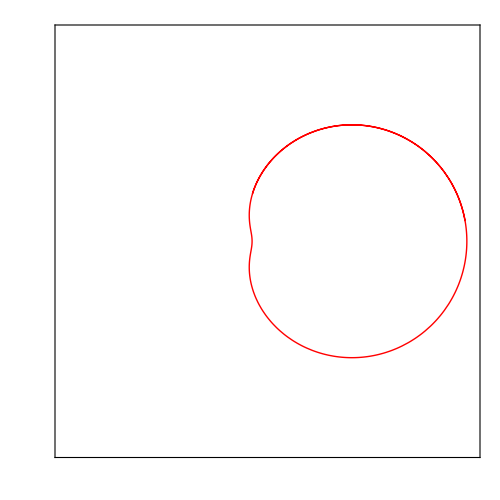

```mathematica
IPolarPerp = PolarPlot[Evaluate[Iperp[r,θ]/NormFactor], {θ,.1,2.6*Pi},PlotStyle-> RGBColor[1,0,0]]
```

I_parvs. θ

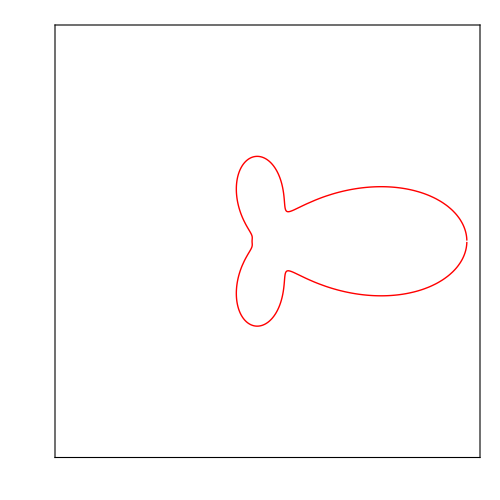

```mathematica
IPolarPar = PolarPlot[Evaluate[Ipar[r,θ]/NormFactor], {θ, π*.001,1.999π},PlotStyle-> RGBColor[1,0,0]]
```

I_unpolvs. θ

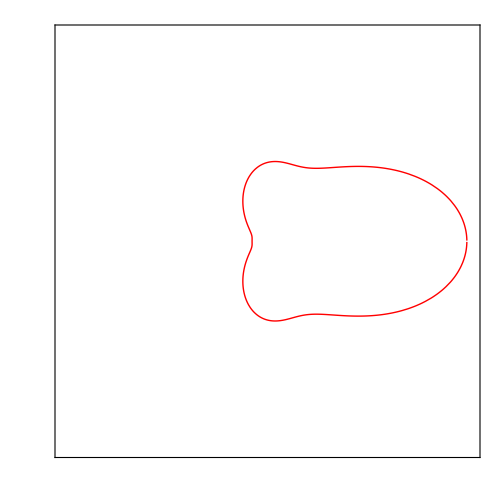

```mathematica
IPolarUnpol = PolarPlot[Evaluate[Iunpol[r,θ]/NormFactor], {θ, π*.001,1.999π},PlotStyle-> RGBColor[1,0,0]]
```

All three on the same plot.  The first expression creates a legend for the plot.

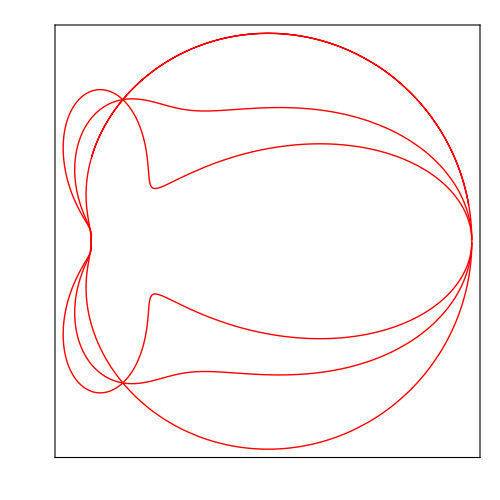

```mathematica
IPolarLegend = {{{RGBColor[1,0,0],"I_perp"},{RGBColor[0,0,1],"I_par"},{RGBColor[0,0,0],"I_unpol"}}, LegendPosition-> {.63,.6}, LegendSize-> {0.25,0.25}, LegendShadow-> {0,0}};
Show[IPolarPerp,IPolarPar,IPolarUnpol, PlotRange-> All,DisplayFunction-> Identity, FrameLabel->{None,None,"Normalized Phase Functions", None} ]
```

#### Log-polar plots of scattered intensity vs. angle.

Begin by defining a few labels and some additional graphics to make the polar plots look good.  Note that I normalize the phase functions to the peak value (which is the same for all polarization states and occurs in the forward direction where θ = 0).

```mathematica
MySpokes = Table[Graphics[Line[{{0,0},{Cos[θ Degree], Sin[θ Degree]}}]], {θ, 0, 345, 30}];
LogRings = Graphics[Table[{Dashing[{0.01,0.01}],Circle[{0,0},Log[10,i]]},{i,1.105171,10,1.1105171}]];
LogNormFactor = NLimit[Log[10,Iperp[r, ϕ]], ϕ-> 0.0, WorkingPrecision-> 20, Terms ->  6];
```

```mathematica
SetOptions[PolarPlot, Frame-> True, PlotRange-> All, ImageSize-> 500,  PlotPoints->30,  AspectRatio-> 1, FrameTicks-> None, Ticks-> None, DisplayFunction-> Identity ];
```

```mathematica
PerpMinValue = FindMinimum[Iperp[r, θ]/NormFactor, {θ,  .75π,π/2}]⟦2,1,2⟧;
ParMinValue = FindMinimum[Ipar[r, θ]/NormFactor, {θ,  .75π,π/2}]⟦2,1,2⟧;
UnpolMinValue = FindMinimum[Iunpol[r, θ]/NormFactor, {θ,  .75π,π/2}]⟦2,1,2⟧;
```

I_perpvs. θ

```mathematica
Timing[ILogPolarPerp = PolarPlot[Evaluate[Log[10,Iperp[r, θ]  + (1-Iperp[r, PerpMinValue])]/LogNormFactor], {θ, 0, 2π}, PlotStyle-> RGBColor[1,0,0], PlotRange-> {{-1,1}, {-1,1}}];]
```

General::ivar: 3.14152 is not a valid variable.

General::stop: Further output of General :: ivar will be suppressed during this calculation.

Power::infy: Infinite expression 1/√0. encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity encountered.

Infinity::indet: Indeterminate expression (0.  + 0.\ ⅈ)\ ComplexInfinity
 encountered.

General::stop: Further output of Infinity :: indet will be suppressed during this calculation.

{0.405,Null}

```mathematica
Show[ILogPolarPerp, MySpokes, LogRings,DisplayFunction-> $DisplayFunction];
```

I_parvs. θ

```mathematica
Timing[ILogPolarPar = PolarPlot[Evaluate[Log[10,Ipar[r, θ]  + (1-Ipar[r, ParMinValue])]/LogNormFactor], {θ, 0, 2π},  PlotStyle-> RGBColor[0,0,1], PlotRange-> {{-1,1}, {-1,1}}];]
```

General::ivar: 3.14178 is not a valid variable.

General::stop: Further output of General :: ivar will be suppressed during this calculation.

Power::infy: Infinite expression 1/√0. encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity encountered.

Infinity::indet: Indeterminate expression (0.  + 0.\ ⅈ)\ ComplexInfinity
 encountered.

General::stop: Further output of Infinity :: indet will be suppressed during this calculation.

{0.406,Null}

```mathematica
Show[ILogPolarPar,  MySpokes, LogRings,DisplayFunction-> $DisplayFunction];
```

I_unpolvs. θ

```mathematica
Timing[ILogPolarUnPol = PolarPlot[Evaluate[Log[10,Iunpol[r, θ]  + (1-Iunpol[r, UnpolMinValue])]/LogNormFactor], {θ, 0, 2π}, PlotStyle-> RGBColor[0,0,0], PlotRange-> {{-1,1}, {-1,1}}];]
```

General::ivar: 3.14158 is not a valid variable.

General::stop: Further output of General :: ivar will be suppressed during this calculation.

Power::infy: Infinite expression 1/√0. encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity encountered.

Infinity::indet: Indeterminate expression (0.  + 0.\ ⅈ)\ ComplexInfinity
 encountered.

General::stop: Further output of Infinity :: indet will be suppressed during this calculation.

{0.515,Null}

```mathematica
Show[ILogPolarUnPol, MySpokes, LogRings,DisplayFunction-> $DisplayFunction];
```

All three on the same plot.  The first expression creates a legend for the plot.

```mathematica
ILogPolarLegend = {{{RGBColor[1,0,0],"I_perp"},{RGBColor[0,0,1],"I_par"},{RGBColor[0,0,0],"I_unpol"}}, LegendPosition-> {.63,.6}, LegendSize-> {0.25,0.25}, LegendShadow-> {0,0}};
ShowLegend[Show[ILogPolarPerp,ILogPolarPar,ILogPolarUnPol,MySpokes, LogRings, PlotRange-> All,DisplayFunction-> Identity, FrameLabel->{None,None,"Log Phase Functions", None} ], ILogPolarLegend,DisplayFunction-> $DisplayFunction ];
```

## Calculate and plot the polarization ratio for unpolarized incident light

Note that this definition applies to an unpolarized incident beam.

```mathematica
PolRatio[a_, θ_]:=(Iperp[a, θ] - Ipar[a, θ])/(Iperp[a, θ] + Ipar[a, θ]);
```

Plot of the polarization ratio vs. angle

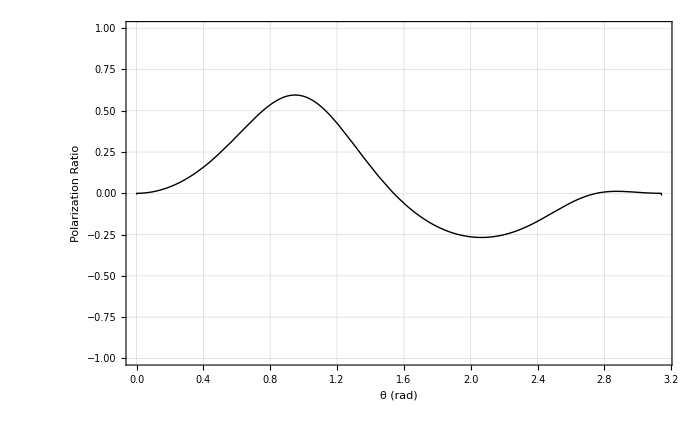

```mathematica
PolRatioPlot = Plot[Evaluate[PolRatio[r, θ]], {θ, 0, π}, Frame-> True, PlotRange-> {-1,1}, ImageSize-> 700, PlotStyle-> RGBColor[0,0,0], GridLines-> Automatic, FrameLabel-> {"θ (rad)","Polarization Ratio", "Polarization Ratio = I_perp/I_perp", None}]
```